## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170608";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
raw=Import[FileNameJoin[{baseDir,eventID,"GR"<>"_IMRP_posterior.csv"}]];
samples["GR"]=(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]](*spin2z*)};
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
evolPlots=<||>
vsPlots=<||>;
vsPlots["p2p4"]={};
```

<||>

## Compute GR m1 and m2 PDF

```mathematica
p="GR"
m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

maxPoint=NMaximize[{m1m2PDF["GR"][x,y],5<x<20&&5<y<20},{x,y}]
m1m2Max=Reverse[Values[maxPoint[[2]]]]
```

GR

输入Mc范围：{3,40}

输入q范围：{1,3}

m1范围：{3.4461,81.9069}

m2范围：{2.04767,45.9479}

对称数据：原始 22641 + 镜像 22641

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

{0.0963773,{x→8.59887,y→9.842}}

{9.842,8.59887}

```mathematica
samples["GR"]
```

Missing[KeyAbsent,GR]

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文_v01\\paper\\submit_final",""}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];
```

```mathematica
(*Export[FileNameJoin[{targetDir,"xxx.pdf"}],evoPlots2[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->80/25.4*72]*)
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_2"}; (*换参数改这里*)
CASE="p2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]],3},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

警告：第 2 个区域点数不足，跳过积分

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2} 预处理完成，红线包含概率 prob = 0.423768

```mathematica
ListLinePlot[contourPoints[CASE]]
```

-Graphics-

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_2}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.288116, 0.711884}

GR 目标区间: {6.28144, 6.42283}

Param 目标区间: {5.45703, 6.31837}

GR下界: 点数=650 | Y>0点数=650 | 平均误差=7.96628×10^-16

GR上界: 点数=650 | Y>0点数=650 | 平均误差=4.67318×10^-16

Param下界: 点数=650 | Y>0点数=650 | 平均误差=8.89545×10^-16

Param上界: 点数=650 | Y>0点数=650 | 平均误差=1.1314×10^-15

{{3.02,27.6173},{3.04,27.8002},{3.06,27.9831},{3.08,28.166},{3.1,28.3489}}

{{3.02,5.41847},{3.04,5.45435},{3.06,5.49024},{3.08,5.52612},{3.1,5.562}}

chi1L取值：0.367177

chi2L取值：0.405346

=====================================================

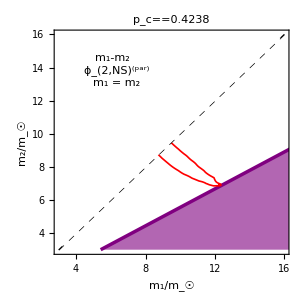

```mathematica
p={"dphi_2"}
probability=prob;
(*probability=0.5;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,16,0.02,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

{dphi_2}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.288116, 0.711884}

GR 目标区间: {6.28144, 6.42283}

Param 目标区间: {5.45703, 6.31837}

GR下界: 点数=370 | Y>0点数=370 | 平均误差=8.64174×10^-16

GR上界: 点数=370 | Y>0点数=370 | 平均误差=4.34487×10^-16

Param下界: 点数=370 | Y>0点数=370 | 平均误差=8.90579×10^-16

Param上界: 点数=370 | Y>0点数=370 | 平均误差=1.12823×10^-15

{{3.1,28.3489},{3.2,29.2634},{3.3,30.1779},{3.4,31.0923},{3.5,32.0068}}

{{3.1,5.562},{3.2,5.74142},{3.3,5.92084},{3.4,6.10026},{3.5,6.27968}}

chi1L取值：0.367177

chi2L取值：0.405346

=====================================================

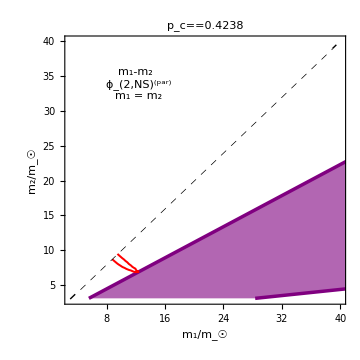

```mathematica
p={"dphi_2"}
probability=prob;
(*probability=0.5;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,40,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_4"}; (*换参数改这里*)
CASE="p4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0553};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0553}，共 2 条

第一条前3点：{{9.32034,9.5699},{9.28847,9.60387},{9.21261,9.68522}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.363336

可信水平百分比：36.3336%

==========================

{dphi_4} 预处理完成，红线包含概率 prob = 0.363336

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

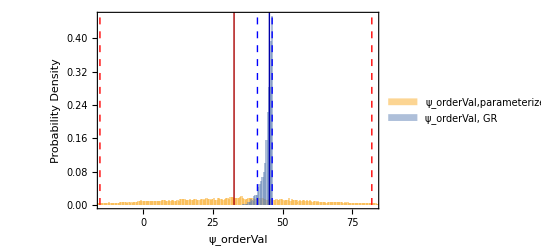

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_4}

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.318332, 0.681668}

GR 目标区间: {44.4664, 45.7982}

Param 目标区间: {19.3698, 45.172}

GR下界: 点数=130 | Y>0点数=130 | 平均误差=2.51423×10^-15

GR上界: 点数=130 | Y>0点数=130 | 平均误差=1.06035×10^-14

Param下界: 点数=130 | Y>0点数=130 | 平均误差=10.7335

Param上界: 点数=130 | Y>0点数=130 | 平均误差=1.00023×10^-14

{{3.1,1.55554×10^6},{3.2,1.60571×10^6},{3.3,1.65589×10^6},{3.4,1.70607×10^6},{3.5,1.75625×10^6}}

{{3.1,1.90059},{3.2,1.9619},{3.3,2.02321},{3.4,2.08452},{3.5,2.14583}}

chi1L取值：0.37315

chi2L取值：0.473781

=====================================================

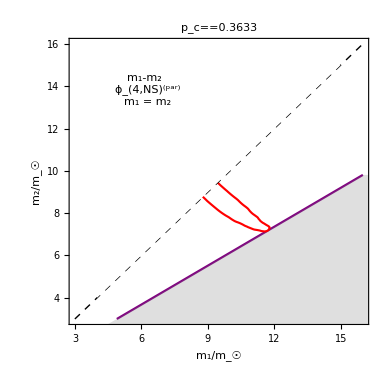

```mathematica
p={"dphi_4"}
probability=prob;
(*probability=0.5;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,16,0.1,cm->True,cd->{1},cu->{0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_5l"}; (*换参数改这里*)
CASE="p5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.063699};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.063699}，共 2 条

第一条前3点：{{9.52037,9.2714},{9.52065,9.27109},{9.54485,9.2484}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.285612

可信水平百分比：28.5612%

==========================

{dphi_5l} 预处理完成，红线包含概率 prob = 0.285612

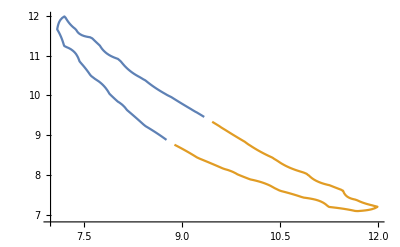

```mathematica
ListLinePlot[contourPoints[p]]
```

{dphi_5l}

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.357194, 0.642806}

GR 目标区间: {465.068, 465.885}

Param 目标区间: {465.581, 553.117}

GR下界: 点数=650 | Y>0点数=650 | 平均误差=2.53609×10^-14

GR上界: 点数=650 | Y>0点数=650 | 平均误差=4.11022×10^-14

Param下界: 点数=650 | Y>0点数=650 | 平均误差=5.72807×10^-14

Param上界: 点数=650 | Y>0点数=650 | 平均误差=71.3442

{{3.02,1.93043},{3.04,1.94322},{3.06,1.956},{3.08,1.96879},{3.1,1.98157}}

{{3.02,288120.},{3.04,290030.},{3.06,291938.},{3.08,293845.},{3.1,295754.}}

chi1L取值：0.356536

chi2L取值：0.434395

=====================================================

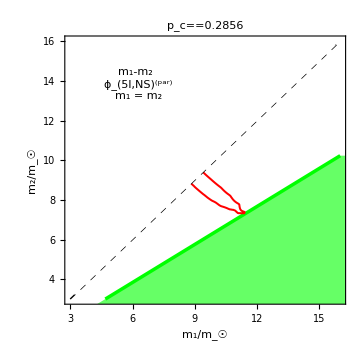

```mathematica
p={"dphi_5l"}
probability=prob;
(*probability=0.28;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,16,0.02,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiLNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_6"}; (*换参数改这里*)
CASE="p6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.227086

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

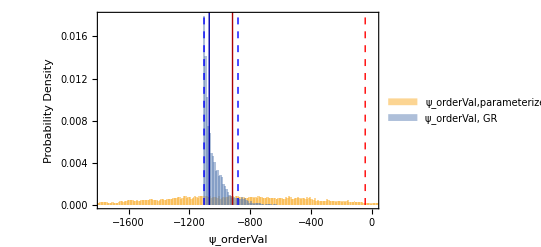

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_6}

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.386457, 0.613543}

GR 目标区间: {-1083.7, -1049.85}

Param 目标区间: {-1079., -755.87}

GR下界: 点数=130 | Y>0点数=130 | 平均误差=1.46918×10^-13

GR上界: 点数=130 | Y>0点数=130 | 平均误差=1.20683×10^-13

Param下界: 点数=130 | Y>0点数=130 | 平均误差=1.24181×10^-13

Param上界: 点数=130 | Y>0点数=130 | 平均误差=4.11022×10^-14

{{3.1,2.17933},{3.2,2.24963},{3.3,2.31994},{3.4,2.39024},{3.5,2.46054}}

{{3.1,14.5861},{3.2,15.0566},{3.3,15.5271},{3.4,15.9976},{3.5,16.4682}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

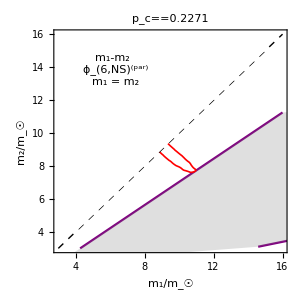

```mathematica
p={"dphi_6"}
probability=prob;
(*probability=0.2;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,16,0.1,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.39519, 0.60481}

实际使用的 GR 概率区间上下界: {-1082.72, -1051.46}

实际使用的 Param 概率区间上下界: {-1067.49, -769.014}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.55417×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.51404×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.14222×10^-13

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=7.10208×10^-14

{{3.01,1.9628},{3.02,1.96932},{3.03,1.97584},{3.04,1.98236},{3.05,1.98889}}

{{3.01,13.5769},{3.02,13.622},{3.03,13.6672},{3.04,13.7123},{3.05,13.7574}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

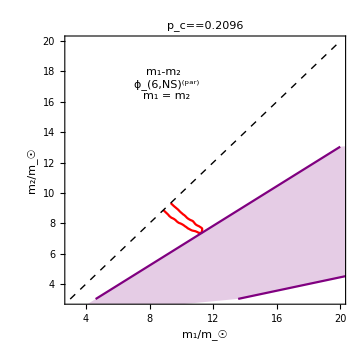

```mathematica
probability=prob;
(*probability=0.37;*)

evolPlots["at"]=PlotInversion[p,probability,3,20,0.01,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.43135, 0.56865}

实际使用的 GR 概率区间上下界: {-1078.95, -1059.18}

实际使用的 Param 概率区间上下界: {-1013.59, -821.238}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.50735×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.09407×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=7.86445×10^-14

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.24788×10^-13

{{3.01,5.98929},{3.02,6.00919},{3.03,6.02909},{3.04,6.04899},{3.05,6.06889}}

{{3.01,11.5067},{3.02,11.545},{3.03,11.5832},{3.04,11.6214},{3.05,11.6596}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

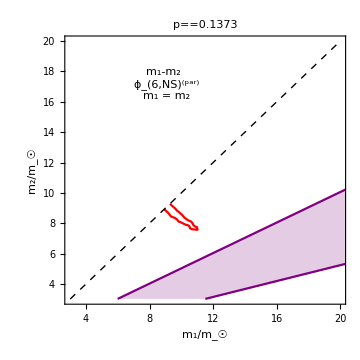

```mathematica
probability=prob;
(*probability=0.26;*)

evolPlots["before"]=PlotInversion[p,probability,3,20,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.36865, 0.63135}

实际使用的 GR 概率区间上下界: {-1085.79, -1045.9}

实际使用的 Param 概率区间上下界: {-1101.82, -731.876}

GR下界: 点数=2500 | Y>0点数=2500 | 平均误差=1.17052×10^-13

GR上界: 点数=2500 | Y>0点数=2500 | 平均误差=1.4752×10^-13

Param下界: 点数=2500 | Y>0点数=2500 | 平均误差=1.44883×10^-13

Param上界: 点数=2500 | Y>0点数=2500 | 平均误差=4.66116×10^-14

{{5.01,5.56839},{5.02,5.57951},{5.03,5.59062},{5.04,5.60173},{5.05,5.61285}}

{{5.01,25.4875},{5.02,25.5383},{5.03,25.5892},{5.04,25.6401},{5.05,25.691}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

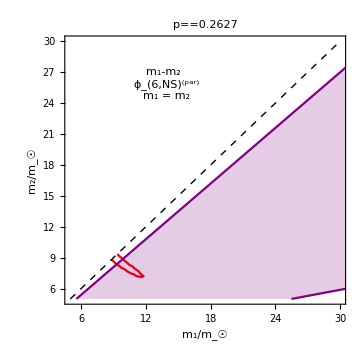

```mathematica
probability=prob;
(*probability=0.5;*)

evolPlots["after"]=PlotInversion[p,probability,5,30,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_dphi6_"<>key<>".pdf"}],evolPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[evolPlots]}]
```

正在导出矢量图: plot_at.pdf ...

正在导出矢量图: plot_before.pdf ...

正在导出矢量图: plot_after.pdf ...

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,20},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];


contourPD[p]={0.0722};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];
```

输入Mc范围：{3,20}

输入q范围：{1,3}

m1范围：{3.4461,40.9535}

m2范围：{2.04767,22.974}

对称数据：原始 19299 + 镜像 19299

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 40.9535} × {2.04767, 40.9535}

等高线值：{0.0722}，共 2 条

第一条前3点：{{9.44055,10.0769},{9.48938,10.1029},{9.51753,10.114}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.00630729

可信水平百分比：0.630729%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.00630729

```mathematica
NMaximize[{m1m2PDF[p][x,y],5<x<20&&5<y<20},{x,y}]
```

{0.0762803,{x→8.09321,y→10.2451}}

{10.2451,8.09321}

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.5, 0.5}

实际使用的 GR 概率区间上下界: {-1069.58, -1069.58}

实际使用的 Param 概率区间上下界: {-916.268, -916.268}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.06598×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.06598×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.29737×10^-13

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.29737×10^-13

{{3.01,8.49909},{3.02,8.52733},{3.03,8.55556},{3.04,8.5838},{3.05,8.61203}}

{{3.01,8.49909},{3.02,8.52733},{3.03,8.55556},{3.04,8.5838},{3.05,8.61203}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

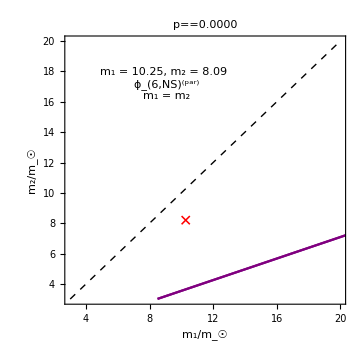

```mathematica
probability=prob;
probability=0.0;

{m1M,m2M}={10.245118127024806,8.093206815313208}

plotp0=PlotInversion[p,probability,3,20,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,
extremePoints->{{m1M,m2M}},extremePointsMarker->"Cross",extremePointsLegend->Row[{Subscript[Style["m",Italic],1]," = 10.25, ",Subscript[Style["m",Italic],2]," = 8.09"}]
,
labelSymbol->Style["p",Italic]]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];


Export[FileNameJoin[{targetDir,eventID<>"_dphi6_"<>"pzero"<>".pdf"}],plotp0,"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500]
```

D:\Documents\workspace\课题\论文\fig\GW170608\GW170608_dphi6_pzero.pdf

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_7"}; (*换参数改这里*)
CASE="p7";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.05};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.05}，共 2 条

第一条前3点：{{9.35133,9.60089},{9.28405,9.6726},{9.27228,9.68522}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.422732

可信水平百分比：42.2732%

==========================

{dphi_7} 预处理完成，红线包含概率 prob = 0.422732

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

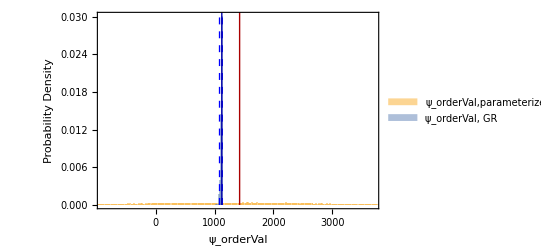

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
0.2927/2
```

0.14635

{dphi_7}

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.4268, 0.5732}

GR 目标区间: {1121.22, 1125.86}

Param 目标区间: {1130.7, 1679.35}

GR下界: 点数=130 | Y>0点数=130 | 平均误差=4.72238×10^-14

GR上界: 点数=130 | Y>0点数=130 | 平均误差=2.79845×10^-14

Param下界: 点数=130 | Y>0点数=130 | 平均误差=2.44864×10^-14

Param上界: 点数=130 | Y>0点数=130 | 平均误差=548.456

{{3.1,2.89047},{3.2,2.98371},{3.3,3.07695},{3.4,3.17019},{3.5,3.26343}}

{{3.1,3.1001},{3.2,3.19993},{3.3,3.30007},{3.4,3.4},{3.5,3.50019}}

chi1L取值：0.365235

chi2L取值：0.434549

=====================================================

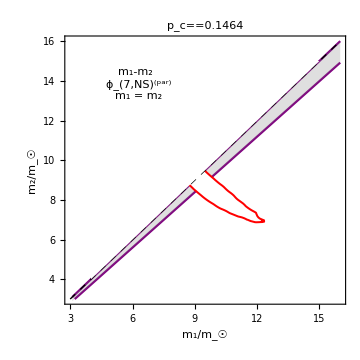

```mathematica
p={"dphi_7"}
probability=prob;
probability=0.1464;

plots[CASE]=PlotMultiInversion[p,{probability},3,16,0.1,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

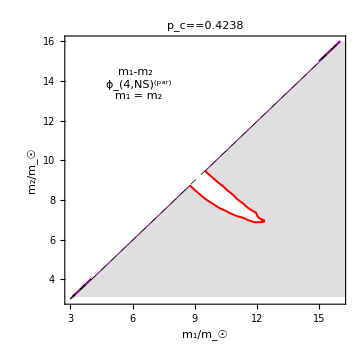
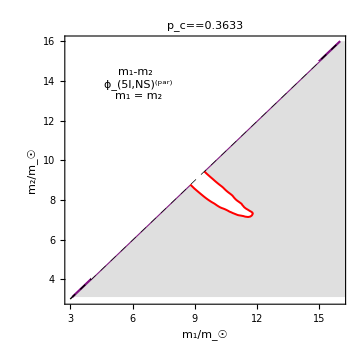
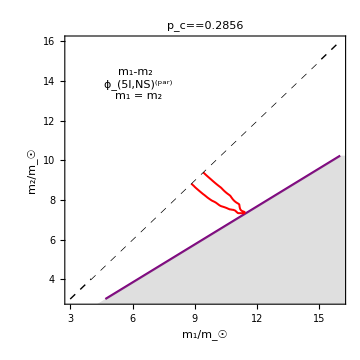
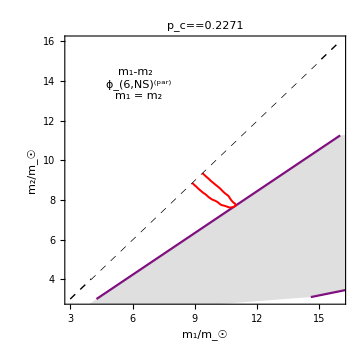
<|p2→-Graphics-,p4→-Graphics-,p5l→-Graphics-,p6→-Graphics-,p7→-Graphics-|>

```mathematica
plots
```

## 5l,4,6,2,7 6 5l,6 4,5l,6 2,4,5l,6 2,4,5l,6,7

```mathematica
evoPlots1=<||>
evoPlots2=<||>
evoPlots3=<||>
evoPlots4=<||>
evoPlots5=<||>
```

<||>

<||>

<||>

«2 more identical outputs»

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_init";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

GR 预处理完成，红线包含概率 prob = 0.227086

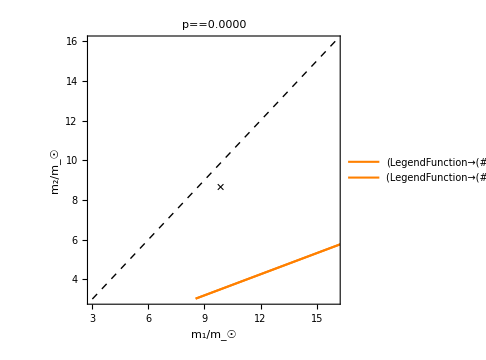

```mathematica
CASE="p6_init";
p={"dphi_6"};
probability=prob;
probability=0.0000;
(*probability=0.2;*)

evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,16,0.02,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{"Points"},
extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,maskM1ltM2->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig1a.pdf"}],evoPlots1[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227,ImageResolution->600]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig1a.pdf

```mathematica
Export[FileNameJoin[{targetDir,"fig1a.svg"}],evoPlots1[CASE],"SVG",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227,ImageResolution->600]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig1a.svg

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.077};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.077}，共 2 条

第一条前3点：{{9.44221,9.19265},{9.4837,9.15362},{9.48837,9.14925}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.173028

可信水平百分比：17.3028%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.173028

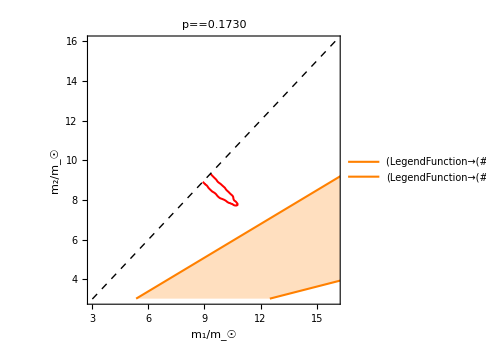

```mathematica
CASE="p6_before";
p={"dphi_6"};
probability=prob;
(*probability=0.0000;*)
(*probability=0.2;*)
evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,16,0.02,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{Automatic},
extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ"},
showVerificationStats->False]
```

```mathematica
Export[FileNameJoin[{targetDir,"fig1b.pdf"}],evoPlots1[CASE],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->227]
```

D:\Documents\workspace\课题\论文_v01\paper\submit_final\fig1b.pdf

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_at";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.227086

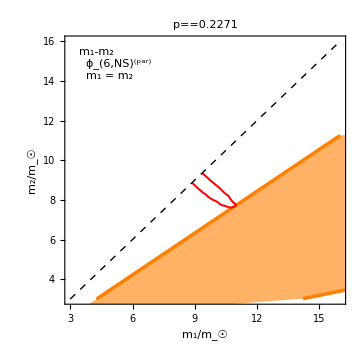

```mathematica
CASE="p6_at";
p={"dphi_6"};
probability=prob;
(*probability=0.0000;*)
(*probability=0.2;*)
evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,16,0.02,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{Automatic},
extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ"},
showVerificationStats->False]
```

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p6_after";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.066};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.066}，共 2 条

第一条前3点：{{9.50691,9.25776},{9.50711,9.25755},{9.54664,9.22047}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.260699

可信水平百分比：26.0699%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.260699

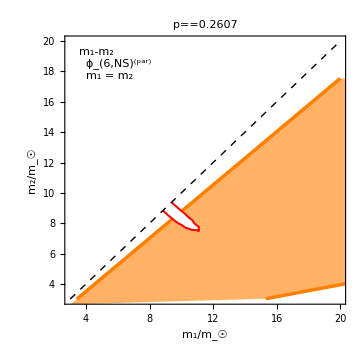

```mathematica
CASE="p6_after";
p={"dphi_6"};
probability=prob;
(*probability=0.0000;*)
(*probability=0.2;*)
evoPlots1[CASE]=PlotMultiInversionWithMode[p,{probability},3,20,0.02,cm->True,cd->{0},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{Automatic},
extremePointsList->{{m1m2Max}},extremePointsMarkerList->{"Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ"},
showVerificationStats->False]
```

### phi_2,6

```mathematica
CASE="p26_init";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.066};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.066}，共 2 条

第一条前3点：{{9.50691,9.25776},{9.50711,9.25755},{9.54664,9.22047}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.260699

可信水平百分比：26.0699%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.260699

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

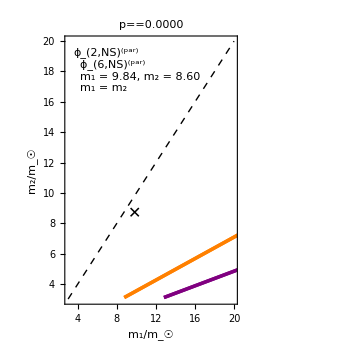

```mathematica
CASE="p26_init";
p={"dphi_2","dphi_6"};
probability=prob;
probability=0.0000;
(*probability=0.2;*)
evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.1,cm->True,cd->{1,1},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{"Points","Points"},
extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

```mathematica
CASE="p26_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.075};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.075}，共 2 条

第一条前3点：{{9.45404,9.20448},{9.48057,9.17952},{9.51286,9.14925}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.190017

可信水平百分比：19.0017%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.190017

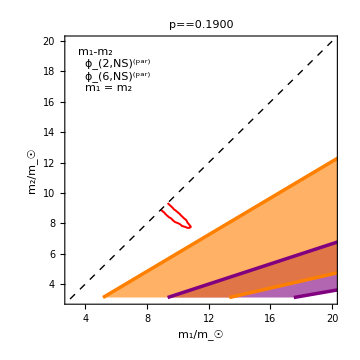

```mathematica
CASE="p26_before";
p={"dphi_2","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.1,cm->True,cd->{1,1},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
(*mode->{"Points","Points"},*)
extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ","Max/Min of α₅ₗ"},
showVerificationStats->False]
```

```mathematica
CASE="p26_at6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.227086

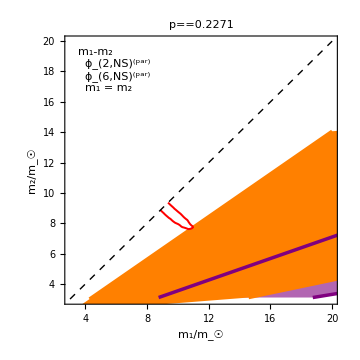

```mathematica
CASE="p26_at6";
p={"dphi_2","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.1,cm->True,cd->{1,0},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
(*mode->{"Points","Points"},*)
extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ","Max/Min of α₅ₗ"},
showVerificationStats->False,
opaqueIndices->{2}]
```

```mathematica
CASE="p26_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.423768

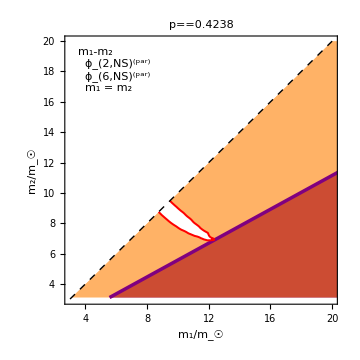

```mathematica
CASE="p26_at2";
p={"dphi_2","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,20,0.1,cm->True,cd->{1,0},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points"},*)
extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ","Max/Min of α₅ₗ"},
showVerificationStats->False,
opaqueIndices->{1}]
```

```mathematica
CASE="p26_after";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.043};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.043}，共 2 条

第一条前3点：{{9.39205,9.64161},{9.35121,9.6851},{9.35024,9.68613}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.49212

可信水平百分比：49.212%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.49212

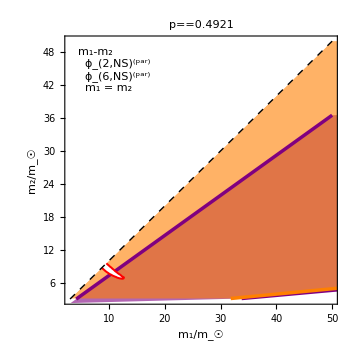

```mathematica
CASE="p26_after";
p={"dphi_2","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots2[CASE]=PlotMultiInversionWithMode[p,{probability,probability},3,50,0.1,cm->True,cd->{1,0},cu->{0,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points"},*)
extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"Max/Min of α₅ₗ","Max/Min of α₅ₗ"},
showVerificationStats->False]
```

### phi_2,4,6

```mathematica
CASE="p246_init";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.066};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.066}，共 2 条

第一条前3点：{{9.50691,9.25776},{9.50711,9.25755},{9.54664,9.22047}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.260699

可信水平百分比：26.0699%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.260699

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_4 模式为 Points，但未提供有效 extremePointsList，已跳过。

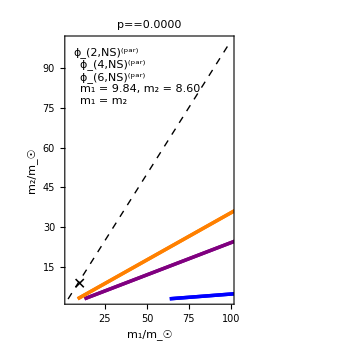

```mathematica
CASE="p246_init";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
probability=0.0000;
(*probability=0.2;*)
evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,100,0.1,cm->True,cd->{1,1,1},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{"Points","Points","Points"},
extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

```mathematica
CASE="p246_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.076};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.076}，共 2 条

第一条前3点：{{9.44813,9.19857},{9.48213,9.16657},{9.50061,9.14925}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.181804

可信水平百分比：18.1804%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.181804

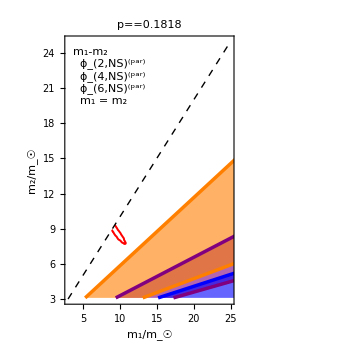

```mathematica
CASE="p246_before";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,1},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
(*mode->{"Points","Points","Points"},*)
extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

```mathematica
CASE="p246_at6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.227086

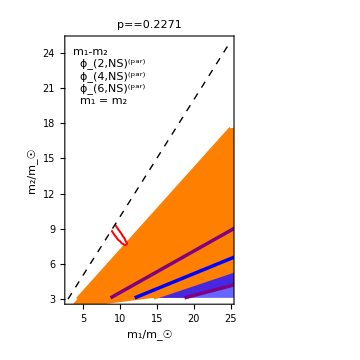

```mathematica
CASE="p246_at6";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,0},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
(*mode->{"Points","Points","Points"},*)
extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{3}]
```

```mathematica
CASE="p246_at4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0553};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0553}，共 2 条

第一条前3点：{{9.32034,9.5699},{9.28847,9.60387},{9.21261,9.68522}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.363336

可信水平百分比：36.3336%

==========================

{dphi_2,dphi_6} 预处理完成，红线包含概率 prob = 0.363336

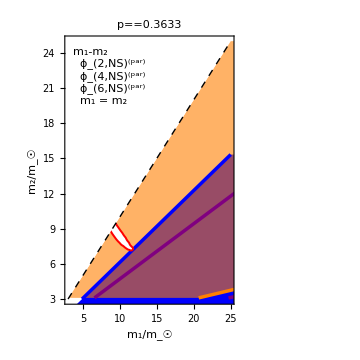

```mathematica
CASE="p246_at4";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,0},cu->{1,0,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Automatic,Automatic},{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points","Points"},*)
extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{2}]
```

```mathematica
CASE="p246_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.423768

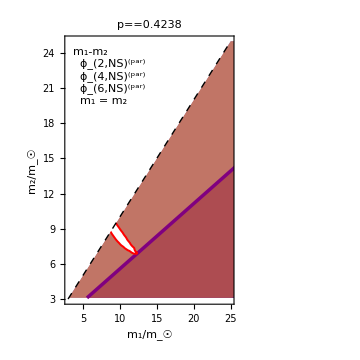

```mathematica
CASE="p246_at2";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,0},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]}},
(*mode->{"Points","Points","Points"},*)
extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{1}]
```

```mathematica
CASE="p246_after";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.044};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.044}，共 2 条

第一条前3点：{{9.38624,9.6358},{9.35177,9.6725},{9.33984,9.68522}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.482271

可信水平百分比：48.2271%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.482271

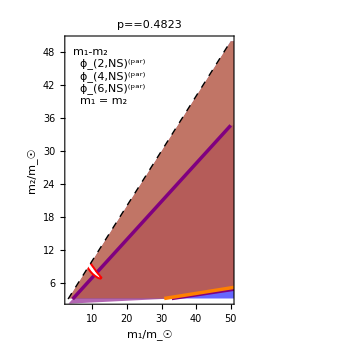

```mathematica
CASE="p246_after";
p={"dphi_2","dphi_4","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots3[CASE]=PlotMultiInversionWithMode[p,{probability,0.4238,probability},3,50,0.1,cm->True,cd->{1,1,0},cu->{0,0,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points","Points"},*)
extremePointsList->{{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross"},extremePointsLegendList->{"","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

### phi_2,4,5l,6

```mathematica
CASE="p245l6_init";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.066};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.066}，共 2 条

第一条前3点：{{9.50691,9.25776},{9.50711,9.25755},{9.54664,9.22047}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.260699

可信水平百分比：26.0699%

==========================

{dphi_2,dphi_4,dphi_6} 预处理完成，红线包含概率 prob = 0.260699

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_4 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_5l 模式为 Points，但未提供有效 extremePointsList，已跳过。

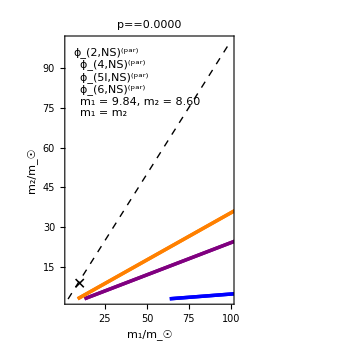

```mathematica
CASE="p245l6_init";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
probability=0.0000;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,100,0.1,cm->True,cd->{1,1,1,1},cu->{1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{"Points","Points","Points","Points"},
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

```mathematica
CASE="p245l6_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.08};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.08}，共 2 条

第一条前3点：{{8.81112,9.06068},{8.80043,9.07801},{8.78077,9.10891}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.140234

可信水平百分比：14.0234%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.140234

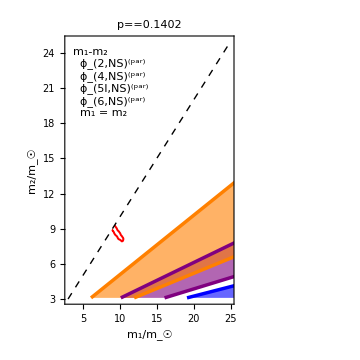

```mathematica
CASE="p245l6_before";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,0,1},cu->{1,1,0,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
(*mode->{"Points","Points","Points","Points"},*)
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

```mathematica
CASE="p245l6_at6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.227086

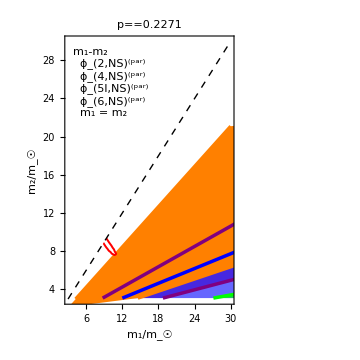

```mathematica
CASE="p245l6_at6";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,30,0.1,cm->True,cd->{1,1,1,0},cu->{1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
(*mode->{"Points","Points","Points","Points"},*)
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{4}]
```

```mathematica
CASE="p245l6_see5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.074};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.074}，共 2 条

第一条前3点：{{9.01154,8.76242},{9.01284,8.76328},{9.02645,8.75402}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.197917

可信水平百分比：19.7917%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.197917

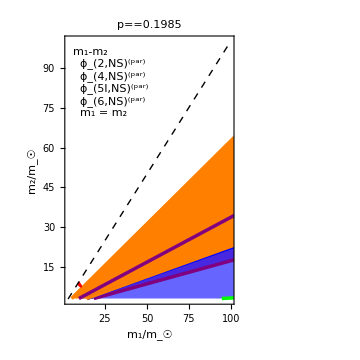

```mathematica
CASE="p245l6_see5l";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
probability=0.1985;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,100,0.2,cm->True,cd->{1,1,1,1},cu->{1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
(*mode->{"Points","Points","Points","Points"},*)
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{4}]
```

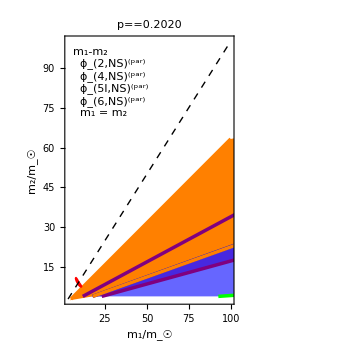

```mathematica
evoPlots4[CASE]
```

```mathematica
CASE="p245l6_at5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.063699};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.063699}，共 2 条

第一条前3点：{{9.52037,9.2714},{9.52065,9.27109},{9.54485,9.2484}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.285612

可信水平百分比：28.5612%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.285612

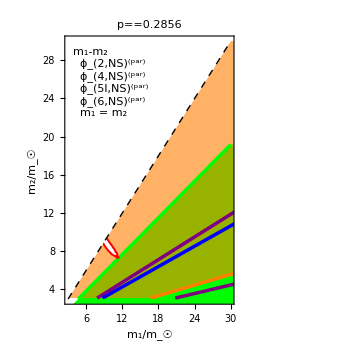

```mathematica
CASE="p245l6_at5l";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,30,0.1,cm->True,cd->{1,1,0,0},cu->{1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Automatic,Automatic},{Automatic,Automatic},{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points","Points","Points"},*)
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{3}]
```

```mathematica
CASE="p245l6_at4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0553};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0553}，共 2 条

第一条前3点：{{9.32034,9.5699},{9.28847,9.60387},{9.21261,9.68522}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.363336

可信水平百分比：36.3336%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.363336

警告：以下样式含 Opacity<1，PDF 导出默认会栅格化：{Directive[Opacity[0.]],Directive[Opacity[0.]],Directive[Opacity[0.]]}。可改用 Lighter[颜色,k]；或导出时使用 Export["fig.pdf", 图, "AllowRasterization" -> False]（以 PDF 透明组输出，仍为矢量）。

Part::pkspec1: The expression i cannot be used as a part specification.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Do::nliter: Non-list iterator If[modeList$399169⟦i⟧==Points,Module[{points$=extremePointsListLocal$399169⟦i⟧,marker$=extremePointsMarkerListLocal$399169⟦i⟧,legendStr$=extremePointsLegendListLocal$399169⟦i⟧,markerGraphics$,markerLegendStyle$,r$=0.8},If[points$===Automatic||points$===None||Length[points$]==0,Print[警告：参数 ,{«4»}⟦i⟧, 模式为 Points，但未提供有效 extremePointsList，已跳过。];Continue[]];If[marker$===Automatic,marker$=Cross];If[legendStr$===Automatic,legendStr$=symbolExprList$399169⟦i⟧];markerGraphics$=Switch[marker$,Cross,{Black,AbsoluteThickness[1.2],Line[Map[«2»]]},Dot,{Black,PointSize[0.03],Point[points$]},_,{Black,PointSize[0.03],Point[points$]}];AppendTo[pointMarkersList$399169,markerGraphics$];markerLegendStyle$=Switch[marker$,Cross,{Black,AbsoluteThickness[1.2],Line[{«2»}]},Dot,{Black,PointSize[0.12],Point[{«1»}]}];AppendTo[legendRows$399169,];]] at position 2 does not evaluate to a real numeric value.

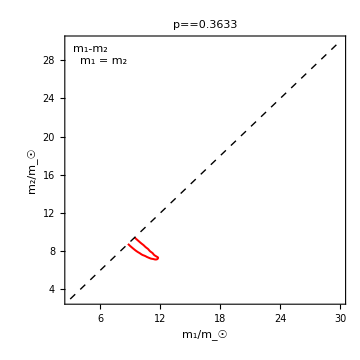

```mathematica
CASE="p245l6_at4";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,30,0.1,cm->True,cd->{1,1,0,0},cu->{1,0,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points","Points","Points"},*)
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{2}]
```

```mathematica
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,30,0.1,cm->True,cd->{1,1,0,0},cu->{1,0,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},labelSymbol->Style["p",Italic],(*★ 必改：Opacity[0.]->None，隐藏线不再进入输出*)lineStyles->{Automatic,{Automatic,Automatic},{None,None},{None,Automatic}},(*★ 新选项：剖面线间距（数据单位），先试 1*)hatchSpacing->1,(*mode->{"Points","Points","Points","Points"},*)extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},showVerificationStats->False,(*★ 语义变化：现控制剖面线颜色对比（2 号原色，其余浅色），需补丁 B*)opaqueIndices->{2}];
```

AppendTo::rvalue: paramFillPolys$405112 is not a variable with a value, so its value cannot be changed.

```mathematica
CASE="p245l6_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.423768

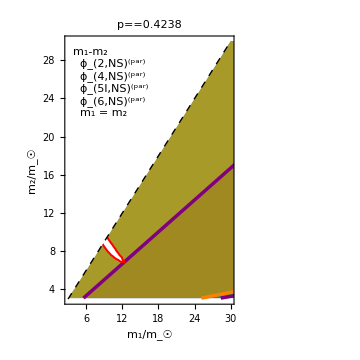

```mathematica
CASE="p245l6_at2";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability},3,30,0.1,cm->True,cd->{1,1,0,0},cu->{1,0,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic},{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points","Points","Points"},*)
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{1}]
```

```mathematica
CASE="p245l6_after";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.042};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.042}，共 2 条

第一条前3点：{{9.39786,9.64742},{9.36392,9.68356},{9.35024,9.69814}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.502653

可信水平百分比：50.2653%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.502653

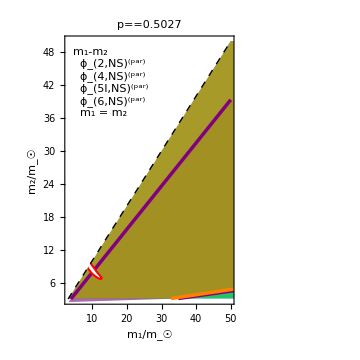

```mathematica
CASE="p245l6_after";
p={"dphi_2","dphi_4","dphi_5l","dphi_6"};
probability=prob;
(*probability=0.2;*)
evoPlots4[CASE]=PlotMultiInversionWithMode[p,{probability,0.4,probability,probability},3,50,0.1,cm->True,cd->{1,1,0,0},cu->{0,0,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{Automatic,{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic},{Directive[Opacity[0.0]],Automatic}},
(*mode->{"Points","Points","Points","Points"},*)
extremePointsList->{{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

### phi_2,4,5l,6,7

```mathematica
CASE="p245l67_init";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6} 预处理完成，红线包含概率 prob = 0.423768

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_4 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_5l 模式为 Points，但未提供有效 extremePointsList，已跳过。

警告：参数 dphi_6 模式为 Points，但未提供有效 extremePointsList，已跳过。

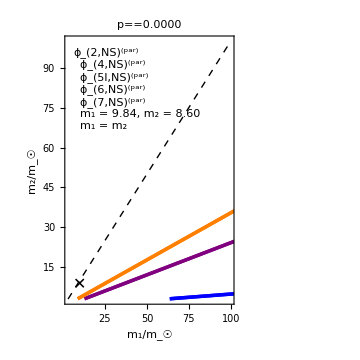

```mathematica
CASE="p245l67_init";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
probability=0.0000;
(*probability=0.2;*)
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,100,0.1,cm->True,cd->{1,1,1,1,1},cu->{1,1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]}},
mode->{"Points","Points","Points","Points","Points"},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False]
```

```mathematica
CASE="p245l67_before";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0835};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0835}，共 2 条

第一条前3点：{{8.84523,9.0912},{8.84024,9.10252},{8.81487,9.14429}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.113109

可信水平百分比：11.3109%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.113109

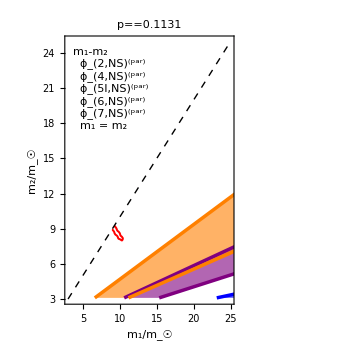

```mathematica
CASE="p245l67_before";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,1,1,0},cu->{1,1,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]}},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{5}]
```

```mathematica
CASE="p245l67_at7";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.079};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.079}，共 2 条

第一条前3点：{{8.80231,9.05187},{8.78399,9.08156},{8.78077,9.08662}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.148209

可信水平百分比：14.8209%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.148209

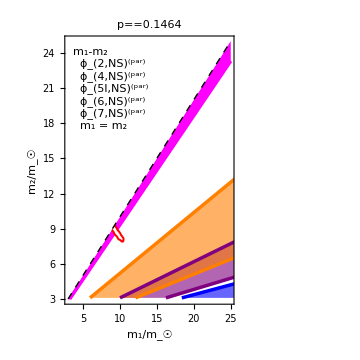

```mathematica
CASE="p245l67_at7";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
probability=0.1464;
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,1,1,0},cu->{1,1,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Directive[Opacity[0.0]]}},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{5}]
```

```mathematica
CASE="p245l67_at6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0702};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0702}，共 2 条

第一条前3点：{{9.48235,9.23288},{9.48239,9.23283},{9.54992,9.16949}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.227086

可信水平百分比：22.7086%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.227086

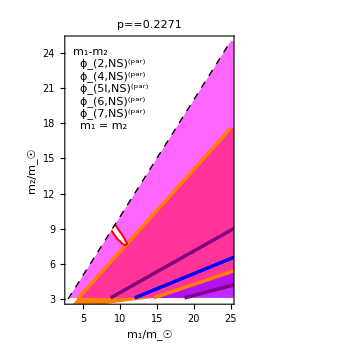

```mathematica
CASE="p245l67_at6";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,1,0,1},cu->{1,1,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Automatic,Directive[Opacity[0.0]]}},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{4}]
```

```mathematica
CASE="p245l67_at5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.063699};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.063699}，共 2 条

第一条前3点：{{9.52037,9.2714},{9.52065,9.27109},{9.54485,9.2484}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.285612

可信水平百分比：28.5612%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.285612

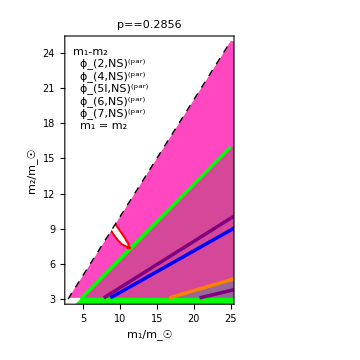

```mathematica
CASE="p245l67_at5l";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,0,0,1},cu->{1,1,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic},{Directive[Opacity[0.0]],Automatic},{Automatic,Directive[Opacity[0.0]]}},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{3}]
```

```mathematica
CASE="p245l67_at4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0553};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0553}，共 2 条

第一条前3点：{{9.32034,9.5699},{9.28847,9.60387},{9.21261,9.68522}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.363336

可信水平百分比：36.3336%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.363336

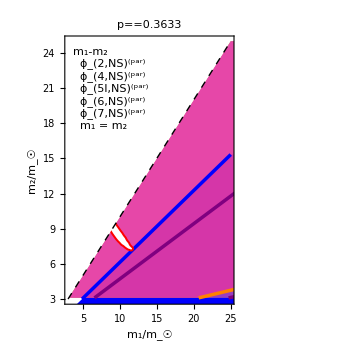

```mathematica
CASE="p245l67_at4";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,0,0,1},cu->{1,0,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Automatic,Automatic},{Directive[Opacity[0.0]],Automatic},{Directive[Opacity[0.0]],Automatic},{Automatic,Directive[Opacity[0.0]]}},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{2}]
```

```mathematica
CASE="p245l67_at2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0499};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0499}，共 2 条

第一条前3点：{{8.61986,8.86942},{8.61602,8.87283},{8.54628,8.93959}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.423768

可信水平百分比：42.3768%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.423768

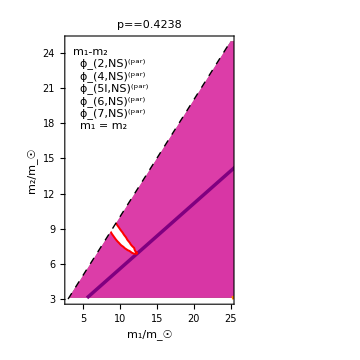

```mathematica
CASE="p245l67_at2";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,25,0.1,cm->True,cd->{1,1,0,0,1},cu->{1,0,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic},{Directive[Opacity[0.0]],Automatic},{Automatic,Directive[Opacity[0.0]]}},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{1}]
```

```mathematica
CASE="p245l67_after";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.041};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.041}，共 2 条

第一条前3点：{{9.40367,9.65323},{9.37663,9.68203},{9.35024,9.71014}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.516328

可信水平百分比：51.6328%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.516328

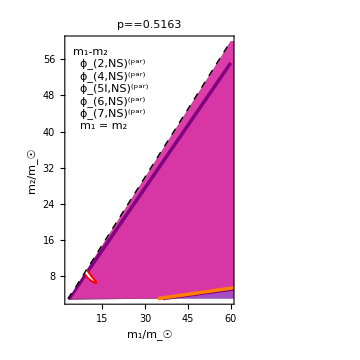

```mathematica
CASE="p245l67_after";
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"};
probability=prob;
(*probability=0.1464;*)
evoPlots5[CASE]=PlotMultiInversionWithMode[p,{probability,probability,probability,probability,probability},3,60,0.1,cm->True,cd->{1,1,0,0,1},cu->{0,0,1,1,0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
lineStyles->{{Automatic,Automatic},{Directive[Opacity[0.0]],Directive[Opacity[0.0]]},{Directive[Opacity[0.0]],Automatic},{Directive[Opacity[0.0]],Automatic},{Automatic,Directive[Opacity[0.0]]}},
extremePointsList->{{},{},{},{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross","Cross","Cross","Cross"},extremePointsLegendList->{"","","","",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->False,
opaqueIndices->{1}]
```

## SAVE

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],evoPlots1[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->400],
{key,Keys[evoPlots1]}]
```

正在导出矢量图: plot_p6_init.pdf ...

正在导出矢量图: plot_p6_before.pdf ...

正在导出矢量图: plot_p6_at.pdf ...

正在导出矢量图: plot_p6_after.pdf ...

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],evoPlots2[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->400],
{key,Keys[evoPlots2]}]
```

正在导出矢量图: plot_p26_init.pdf ...

正在导出矢量图: plot_p26_before.pdf ...

正在导出矢量图: plot_p26_at6.pdf ...

正在导出矢量图: plot_p26_at2.pdf ...

正在导出矢量图: plot_p26_after.pdf ...

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],evoPlots3[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->400],
{key,Keys[evoPlots3]}]
```

正在导出矢量图: plot_p246_init.pdf ...

正在导出矢量图: plot_p246_before.pdf ...

正在导出矢量图: plot_p246_at6.pdf ...

正在导出矢量图: plot_p246_at4.pdf ...

正在导出矢量图: plot_p246_at2.pdf ...

正在导出矢量图: plot_p246_after.pdf ...

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],evoPlots4[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->400],
{key,Keys[evoPlots4]}]
```

正在导出矢量图: plot_p245l6_at6.pdf ...

正在导出矢量图: plot_p245l6_atgreen.pdf ...

Export::noopen: Cannot open D:\Documents\workspace\课题\论文\fig\GW170608\GW170608_p245l6_atgreen.pdf.

正在导出矢量图: plot_p245l6_see5l.pdf ...

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],evoPlots5[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->400],
{key,Keys[evoPlots5]}]
```

正在导出矢量图: plot_p245l67_init.pdf ...

正在导出矢量图: plot_p245l67_before.pdf ...

正在导出矢量图: plot_p245l67_at7.pdf ...

正在导出矢量图: plot_p245l67_at6.pdf ...

正在导出矢量图: plot_p245l67_at5l.pdf ...

正在导出矢量图: plot_p245l67_at4.pdf ...

正在导出矢量图: plot_p245l67_at2.pdf ...

正在导出矢量图: plot_p245l67_after.pdf ...

# utils